## This notebook examined the Hubble constant to see if it has any affect on fitting the differential burst rate at different redshift and jet opening angle distributions

```mathematica
$Line=0;Clear["Global`*"];
```

```mathematica
Off[NIntegrate::slwcon]
```

```mathematica
Off[NIntegrate::nlim]
```

```mathematica
Off[FindRoot::nlnum]
```

```mathematica
Off[ReplaceAll::reps]
```

```mathematica
SetDirectory["/Users/tle/Research/Hubble.Constant/paper2/calculation"]
```

/Users/tle/Research/Hubble.Constant/paper2/calculation

### Below are functions that takes any data values and turns into a cumulative distribution & different KS test functions.

Below is function that takes any data values and turns into a cumulative distribution.

```mathematica
Clear[CumulativeFunc,datalistA]
```

```mathematica
CumulativeFunc[datalistA_]:=Module[{cumdata={},i,imax,datai},
imax=Length[datalistA];
datalist=Sort[datalistA];
For[i=0.0,i<imax,
datai=i/imax;
cumdata=Append[cumdata,{datalist[[i+1]],datai}];
datai=(i+1.)/imax;
cumdata=Append[cumdata,{datalist[[i+1]],datai}];
i++];
Return[cumdata];]
```

Next, I have a probability Kolmogorov-Smirnov (KS) Test function

```mathematica
Clear[probKSfunc,Alam]
```

```mathematica
probKSfunc[Alam_]:=Module[{eps1=10^-3.,eps2=10^-8.,
a2,fac,probks,termbf,term,j,i},
a2=-2*Alam^2;
fac=2.;
probks=0.0;
termbf=0.0;
i=0;
For[j=1,j<100,
term=fac*Exp[a2*j^2];
probks=probks+term;
If[Abs[term]≤ (eps1*termbf) || Abs[term]≤ (eps2*probks),
j=101;i=1;];
fac=-fac;
termbf=Abs[term];
j++];
If[i==0,Return[1],Return[probks]];]
```

Next, I have a two data set KS test function

```mathematica
Clear[KStwoTest,data1,data2]
```

```mathematica
KStwoTest[data1_,data2_]:=Module[{n1,en1,n2,en2,j1,j2,fn1,fn2,d1,d2,Dstatistic,Dt,prob,Sdata1,Sdata2,en},
n1=Length[data1];
en1=n1;
n2=Length[data2];
en2=n2;
Sdata1=Sort[data1];
Sdata2=Sort[data2];
j1=1.0;
j2=1.0;
fn1=0.0;
fn2=0.0;
Dstatistic=0.0;
While[j1≤n1 && j2 ≤ n2,
d1=Sdata1[[j1]];
d2=Sdata2[[j2]];
If[d1 ≤ d2,
fn1=j1/en1;
j1=j1+1;];
If[d2≤d1,
fn2=j2/en2;
j2=j2+1;];
Dt=Abs[fn2-fn1];
If[Dt>Dstatistic,Dstatistic=Dt;val={d1,d2};];
];
en=Sqrt[(en1*en2)/(en1+en2)];
prob=probKSfunc[((en+0.12)+(0.11/en))Dstatistic];
Return[{val,Dstatistic,prob}];]
```

Next, I have a one data set and a function KS test function

```mathematica
Clear[KSoneTest,dataVal,Modelfunc]
```

```mathematica
KSoneTest[dataVal_,Modelfunc_]:=Module[{SdataVal,n1,en,Dstatistic,f0,fn,ff,Dist,prob,val},
SdataVal=Sort[dataVal];
n1=Length[SdataVal];
en=n1;
Dstatistic=0.0;
f0=0.0;
For[j=1,j<n1+1,
fn=j/en;
ff=Modelfunc[dataVal[[j]]];
Dist=Max[Abs[f0-ff],Abs[fn-ff]];
If[Dist > Dstatistic,Dstatistic=Dist;val=SdataVal[[j]];];
f0=fn;
j++];
en=Sqrt[en];
prob=probKSfunc[((en+0.12)+(0.11/en))Dstatistic];
Return[{val,Dstatistic,prob}];]
```

Next, I have a function that extract the independent variable x  of (x,y).

```mathematica
Clear[ExtractFunc,datalist]
```

```mathematica
ExtractFunc[datalist_]:=Module[{i,j=0,datax={},n1},
n1=Length[datalist]/2;
For[i=1,i<n1+1,
j=j+1;
datax=Append[datax,datalist[[j]][[1]]];
j=j+1;
i++];
Return[datax];]
```

Next, I have the cummulative function distribution interpolated so that 
I can use it to do a KSone test.

```mathematica
Clear[InterpolatecumFunc,datalist]
```

```mathematica
InterpolatecumFunc[datalist_]:=Module[{n1,cumfunc},
n1=Length[datalist];
cumfunc=Interpolation[datalist];
Return[cumfunc];]
```

### Observational Data from preSwift Era

#### Next is the updated preSwift redshift distribution from Friedman & Bloom (2005)

```mathematica
preSwiftRedshift={0.8349,0.9578,3.418,1,2.5,1.0969,0.9662,1.5,1.6004,1.6187,0.8424,0.4331,0.7055,1.02,4.5,0.8463,2.0335,1.1182,1.5,1.0585,2.0369,1.4769,0.4509,0.362,2.14,3.198,0.6899,2.3,1.254,2.3351,1.006,1.986,3.3718,1.52,0.1685,2.6564,1,2.1,1.5,0.859,0.716};
```

Sort out the "SwiftPerleyRedshift"  data above using Mathematica "Sort" command to get the 
    redshift from smallest to largest redshift (this will give you an idea the range of the redshift)

```mathematica
Sort[preSwiftRedshift,Less]
```

{0.1685,0.362,0.4331,0.4509,0.6899,0.7055,0.716,0.8349,0.8424,0.8463,0.859,0.9578,0.9662,1,1,1.006,1.02,1.0585,1.0969,1.1182,1.254,1.4769,1.5,1.5,1.5,1.52,1.6004,1.6187,1.986,2.0335,2.0369,2.1,2.14,2.3,2.3351,2.5,2.6564,3.198,3.3718,3.418,4.5}

```mathematica
nlength =Length[preSwiftRedshift]
```

41

Next, we create a cumulative preSwift redshift distribution data

```mathematica
Clear[preSwiftRedshiftDist]
```

```mathematica
preSwiftRedshiftDist=CumulativeFunc[preSwiftRedshift];
```

Next, we plot the preSwift redshift distribution

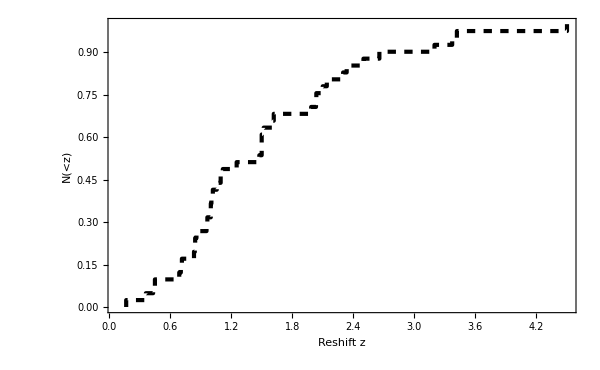

```mathematica
preSwiftRedshiftDistPlot=ListPlot[preSwiftRedshiftDist,PlotRange->All,Joined->True,PlotStyle->{Hue[0.,0,0],Dashing[{.01}],Thickness[0.005]},
Frame->True,Axes->False,FrameLabel->{"Reshift z","N(<z)","",""},BaseStyle->{FontSize->18},ImageSize->600]
```

Use the Mathematica "BinCounts" to determine the total redshift  frequency per bin with 
    a bin size roughly about 1 going from 0 to 5.  Change the bin size until the mean of the 
    distribution is around 1.5 as according to the preSwift redshift distribution curve above. These data points
    represent the differential burst rate per redshift.

```mathematica
Clear[zmin,zmax,Nsamples,delz]
{zmin=0,zmax=5.,Nsamples=5,delz=(zmax-zmin)/Nsamples}
```

{0,5.,5,1.}

```mathematica
Clear[redshiftFreq]
redshiftFreq=BinCounts[preSwiftRedshift,{zmin,zmax,delz}]
```

{13,16,8,3,1}

```mathematica
Clear[sizedata,difBurstRate,midPointRedshift,redshift]
sizedata={};difBurstRate=0;midPointRedshift=0;redshift=0;
For[i=1,i≤Nsamples,
difBurstRate=(redshiftFreq[[i]]);
redshift=(i-1)*delz;
midPointRedshift=(redshift+i*delz)/2;
sizedata=Append[sizedata,{midPointRedshift,difBurstRate}];
i++]
sizedata
```

{{0.5,13},{1.5,16},{2.5,8},{3.5,3},{4.5,1}}

```mathematica
Mean[preSwiftRedshift]
```

1.52873

Find a function that fits through these data point and calculate the area under the curve to normalize 
the differential burst rate per redshift curve.

```mathematica
line=Fit[sizedata,{1,x,x^2,x^3},x]
```

7.0125+16.7083 x-9.25 x^2+1.16667 x^3

```mathematica
Integrate[line,{x,0,4.5}]
```

39.3609

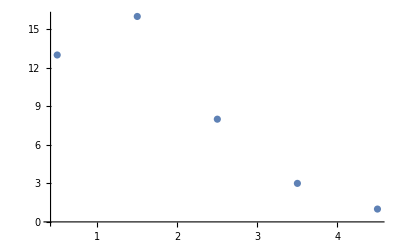

```mathematica
PlotData=ListPlot[{sizedata},PlotRange->All]
```

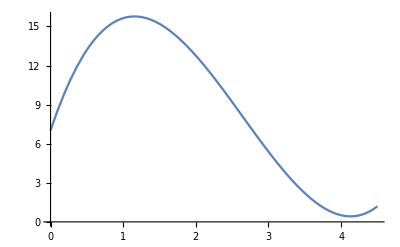

```mathematica
PlotFit=Plot[line,{x,0,4.5}]
```

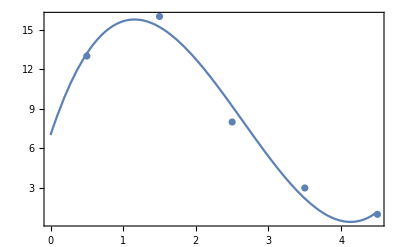

```mathematica
Show[PlotData,PlotFit,PlotRange->All,Frame->True,Axes->False]
```

normalize the differential burst rate per redshift curve.

```mathematica
Clear[sizedata,difBurstRate,midPointRedshift,redshift,ErrorOfR]
sizedata={};difBurstRate=0;midPointRedshift=0;redshift=0;ErrorOfR={};

For[i=1,i≤Nsamples,
difBurstRate=(redshiftFreq[[i]]);
redshift=(i-1)*delz;
midPointRedshift=(redshift+i*delz)/2;
normConst = Integrate[line,{x,0,4.5}];
sizedata=Append[sizedata,{midPointRedshift,difBurstRate/normConst}];
errorBar = Sqrt[difBurstRate]/2.;
MinusErrorOfR=(difBurstRate-errorBar)/normConst;
PlusErrorOfR=(difBurstRate+errorBar)/normConst;
ErrorOfR=Append[ErrorOfR,{{midPointRedshift,MinusErrorOfR},{midPointRedshift,PlusErrorOfR}}];
i++]
sizedata
ErrorOfR
```

{{0.5,0.330277},{1.5,0.406494},{2.5,0.203247},{3.5,0.0762177},{4.5,0.0254059}}

{{{0.5,0.284476},{0.5,0.376078}},{{1.5,0.355683},{1.5,0.457306}},{{2.5,0.167318},{2.5,0.239177}},{{3.5,0.0542155},{3.5,0.0982199}},{{4.5,0.0127029},{4.5,0.0381088}}}

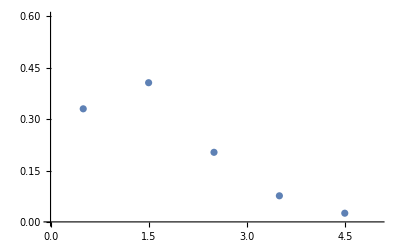

```mathematica
Clear[PlotData]
PlotData=ListPlot[sizedata,PlotRange->{{0,5},{0,0.6}}]
```

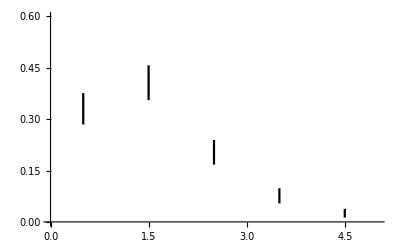

```mathematica
Clear[PlotError]
PlotError=ListPlot[ErrorOfR,Joined->True,PlotStyle->{Black},PlotRange->{{0,5},{0,0.6}}]
```

```mathematica
redshiftLabel1 := Graphics[{Text["(a)",{4.7,0.48}],Text["preSwift",{4.5,0.44}]}];
```

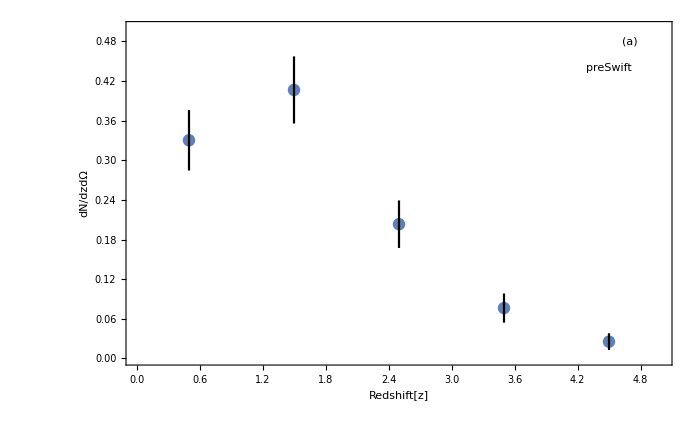

```mathematica
preSwiftBurstRatePerRedshiftPlot =Show[PlotData,PlotError,redshiftLabel1,FrameLabel->{"Redshift[z]","dṄ/dzdΩ ",""," "},BaseStyle->{FontSize->18},ImageSize->700,Frame->True,PlotRange->{{0,5},{0,0.5}}]
```

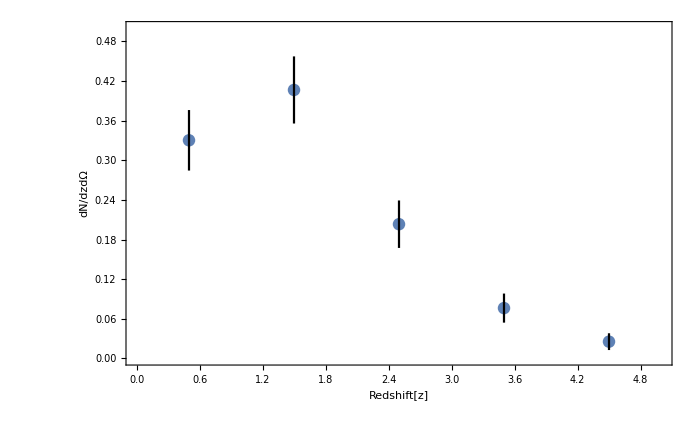

```mathematica
dataPlot =Show[PlotData,PlotError,FrameLabel->{"Redshift[z]","dṄ/dzdΩ ",""," "},BaseStyle->{FontSize->18},ImageSize->700,Frame->True,PlotRange->{{0,5},{0,0.5}}]
```

## Model: Comoving Density follows the Star Formation Rate (SFR)

```mathematica
{OmegaM=0.27, OmegaL=0.73,h0=10^5 * 1/(10^6 *3.1*10^18),H0=72*h0}
```

{0.27,0.73,3.22581×10^-20,2.32258×10^-18}

```mathematica
{p0=0.,q0=0.,c=3*10^10.,deltstar0=10.,Estar0=5 10^50.,NdensityVal0=1.1574*10^(-89)}
```

{0.,0.,3.×10^10,10.,5.×10^50,1.1574×10^-89}

Next, I define the Hubble function and the distance luminosity

```mathematica
Clear[Hfunc,dLum]
```

```mathematica
Hfunc[z_,H_]=H Sqrt[OmegaM(1.0+z)^3. +OmegaL]
```

H √(0.73+0.27 (1.+z)^3.)

```mathematica
Hfunc[1,H0]
```

3.94839×10^-18

```mathematica
dLum[z_,H_]:=c (1.0+z)NIntegrate[1/Hfunc[z1,H],{z1,0,z}]
```

```mathematica
dLum[1,H0]
```

2.02963×10^28

Next, I define the comoving density  of GRB follows the Star Formation Rate (SFR);
sfr=1 for constant comoving density; sfr=2 is SFR of Lower SFR (Dermer 2006);
sfr=3 is SFR parametric fitting to the form  of Cole et al. (2001) used by  
Baldry & Glazebrook(2003) and Hopkins& Beacom (2006);   sfr=4 is SFR of Upper SFR (Dermer 2006); 
 sfr=5 is a modification SFR of Hopkins & Beacom to attain a constant comoving rate-density at high redshift z;
 sfr=6 is a modification SFR of Hopkins & Beacom to attain a monotonically increasing comoving rate-density 
 with increasing redshift.

Normalizing the comoving density to 1 at  z=0 .

```mathematica
Clear[NdensityFunc,sfr,z]
```

```mathematica
NdensityFunc[sfr_,z_]:=Module[{Ndensity,a,b,c,d,z1,par1,par2,par3,par4,par1a,par2a,par3a,par1b,par2b,par3b,par4b,m1,b1,m2,b2,m3,b3,h=.7,valz0,val},

This model 7 is using equation [16]

If[sfr==7,
par1=0.0157;par2=0.118;par3=3.23;par4=4.66;
Ndensity[z1_]:=(par1+par2*z1)/(1+(z1/par3)^par4) ;
valz0=Ndensity[0];
val=Ndensity[z]/valz0;];

This model 9 is using equation [18]

If[sfr==9,a=1.0;alpha=4.1;beta=0.8;gamma=-5.1;z1val=0.5;z2val=4.5;
b=a(1+z1val)^alpha/(1.0+z1val)^beta;
c=b(1+z2val)^beta/(1.0+z2val)^gamma;
Ndensity[z1_]:=a(1.0+z1)^alpha/;0≤z1≤z1val;
Ndensity[z1_]:=b(1.0+z1)^beta/;z1val<z1≤z2val;
Ndensity[z1_]:=c(1.0+z1)^gamma/;z1>z2val;
valz0=Ndensity[0];
val=Ndensity[z]/valz0;];

If[sfr==11,a=1.0;alpha=5.5;beta=0.38;gamma=-4.1;z1val=0.5;z2val=4.5;
b=a(1+z1val)^alpha/(1.0+z1val)^beta;
c=b(1+z2val)^beta/(1.0+z2val)^gamma;
Ndensity[z1_]:=a(1.0+z1)^alpha/;0≤z1≤z1val;
Ndensity[z1_]:=b(1.0+z1)^beta/;z1val<z1≤z2val;
Ndensity[z1_]:=c(1.0+z1)^gamma/;z1>z2val;
valz0=Ndensity[0];
val=Ndensity[z]/valz0;];

Return[val];]
```

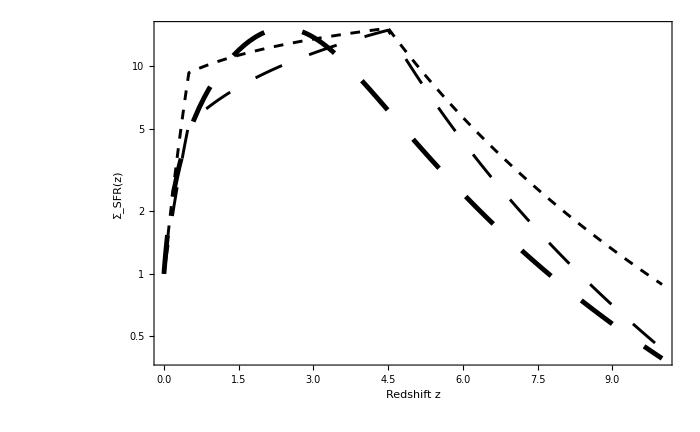

```mathematica
fig1b=LogPlot[{NdensityFunc[7,z],NdensityFunc[9,z],NdensityFunc[11,z]},{z,0,10},PlotRange->All,PlotPoints->100,PlotStyle->{{Hue[0,0,0],Dashing[{.04}],Thickness[.005]},
{Hue[0,0,0],Dashing[{.03}],Thickness[.003]},
{Hue[0,0,0],Dashing[{.01}],Thickness[.003]}},Frame->True,FrameLabel->{"Redshift z","Σ_SFR(z)"," "," "},ImageSize->700]
```

```mathematica
SFRlabel1 := Graphics[{Text["(b)",{9.7,2.3}],Text[" SFR 7 ",{4,1.5}],Text[" 11 ",{8,1.}],Text[" 9 ",{1.5,1.7}]}];
```

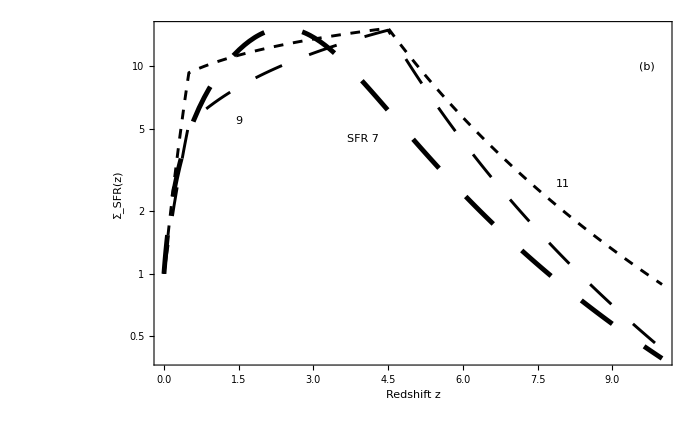

```mathematica
figure1b=Show[fig1b,SFRlabel1,BaseStyle->{FontSize->22},ImageSize->700]
```

### Next, I determine the maximum z for which GRB is too far to observed for a given jet opening angle.

below is the nu fnu low and high energy indices

```mathematica
Clear[k1,OpeningAngleFunc,thetaRad,deltstar,fthres,fThresSwiftVal0,fThresPreSwiftVal0]
```

```mathematica
{fThresSwiftVal0=10^-8.,fThresPreSwiftVal0=10^-7.};
```

```mathematica
OpeningAngleFunc[thetaRad_,Estar_,deltstar_,fthres_,k1_]=10^-56.Estar (4Pi (1-Cos[thetaRad])*deltstar* k1* fthres)^-1;
```

```mathematica
Clear[ZlimitFunc]
```

```mathematica
ZlimitFunc[thetaRad_,zmin_,zmax_,H_,Estar_,delstar_,fthres_,k1_]:=Module[{val},
val=z2/.FindRoot[10^-56 dLum[z2,H]^2==OpeningAngleFunc[thetaRad,Estar,delstar,fthres,k1],{z2,zmin,zmax},MaxIterations->40];
Return[val];];
```

Next, I define the predicted burst rate or the differential number of sources per unit redshift z per solid angle.

```mathematica
Clear[dNdzdOmega,Qfunc,YminFunc]
```

```mathematica
Qfunc[z_,H_,Estar_,deltstar_,fthres_,k1_]:=Estar (4.Pi dLum[z,H]^2. deltstar k1 fthres)^-1.
```

```mathematica
YminFunc[z_,mujMin_,H_,Estar_,deltstar_,fthres_,k1_]:=Min[1.0-mujMin,Qfunc[z,H,Estar,deltstar,fthres,k1]];
```

```mathematica
dNdzdOmega[z_,thetajRadMin_,thetajRadMax_,s_,H_,Estar_,deltstar_,fthres_,sfr_,Ndensity0_,k1_]:=Module[{val,zthres,mujMin,mujMax},
mujMin=Cos[thetajRadMax];
mujMax=Cos[thetajRadMin];
zthres=ZlimitFunc[thetajRadMin,0.,20.,H,Estar,deltstar,fthres,k1];
val:=c dLum[z,H]^2. Ndensity0 NdensityFunc[sfr,z]/((1.+z)^3.0 Hfunc[z,H])(1.+s)/(2.+s)
(YminFunc[z,mujMin,H,Estar,deltstar,fthres,k1]^(2.+s)-(1.-mujMax)^(2.+s))/((1.-mujMin)^(1.+s)-(1.-mujMax)^(1.+s))/;z≤zthres; 
val:=0/;z>zthres;
Return[val];];
```

### The next function assumes a delta function in the jet's opening angle

```mathematica
Clear[dNdzdOmega1]
```

```mathematica
dNdzdOmega1[z_,thetaj_,s_,H_,Estar_,deltstar_,fthres_,sfr_,Ndensity0_,k1_]:=Module[{val,zthres},
zthres=ZlimitFunc[thetaj,0.,20.,H,Estar,deltstar,fthres,k1];
mujbar=Cos[thetaj];
val:=c dLum[z,H]^2. Ndensity0 NdensityFunc[sfr,z]/((1.+z)^3. Hfunc[z,H])(1.+s)(1.-mujbar)^(s+1.)/;z≤zthres;
val:=0/;z>zthres;
Return[val];];
```

### Next, I integrate the GRB redshift distribution. There is energy indices (a and b) dependency for the jet’s opening angle distribution function

```mathematica
Clear[dNdzdOmegaFunc]
```

```mathematica
dNdzdOmegaFunc[zmin_,zmax_,thetajRadMin_,thetajRadMax_,s_,H_,Estar_,deltstar_,fthres_,sfr_,Ndensity0_,k1_]:=Module[{val},
val=NIntegrate[dNdzdOmega[zval,thetajRadMin,thetajRadMax,s,H,Estar,deltstar,fthres,sfr,Ndensity0,k1],{zval,zmin,zmax},MinRecursion->1,MaxRecursion->20,AccuracyGoal->16];
Return[val];];
```

```mathematica
Clear[NdotcoConst,dNdOmegaFunc]
```

```mathematica
NdotcoConst[zmin_,zmax_,thetajRadMin_,thetajRadMax_,s_,H_,Estar_,deltstar_,fthres_,sfr_,Ndensity0_,eta_,k1_]:= (eta*10.^-6)/dNdzdOmegaFunc[zmin,zmax,thetajRadMin,thetajRadMax,s,H,Estar,deltstar,fthres,sfr,Ndensity0,k1]
```

Size distribution calculation

```mathematica
dNdOmegaFunc[zmin_,thetajRadMin_,thetajRadMax_,s_,H_,Estar_,deltstar_,fthres_,sfr_,Ndensity0_,k1_]:=Module[{val},
zmax=ZlimitFunc[thetajRadMin,0.,20.,H,Estar,deltstar,fthres,k1];
val=dNdzdOmegaFunc[zmin,zmax,thetajRadMin,thetajRadMax,s,H,Estar,deltstar,fthres,sfr,Ndensity0,k1];
Return[val]];
```

The next function assumes a delta function in the jet's opening angle

```mathematica
Clear[dNdzdOmegaFunc1]
```

```mathematica
dNdzdOmegaFunc1[zmin_,zmax_,thetajRad_,s_,H_,Estar_,deltstar_,fthres_,sfr_,Ndensity0_,k1_]:=Module[{val},
val=NIntegrate[dNdzdOmega1[z,thetajRad,s,H,Estar,deltstar,fthres,sfr,Ndensity0,k1],{z,zmin,zmax},
MinRecursion->1,MaxRecursion->20,AccuracyGoal->16];
Return[val];];
```

```mathematica
Clear[RedshiftCumulativeFunc]
```

```mathematica
RedshiftCumulativeFunc[thetajMinRad_,thetajMaxRad_,zmaxL_,s_,H_,Estar_,deltstar_,fthres_,sfr_,Ndensity0_,Nsamples_,k1_]:=Module[{zmin,val,datalist,delz},
zmin=10^-4.;
zmax=ZlimitFunc[thetajMinRad,0.,20.,H,Estar,deltstar,fthres,k1];
delz=(zmaxL-zmin)/Nsamples;
val=dNdzdOmegaFunc[zmin,zmax,thetajMinRad,thetajMaxRad,s,H,Estar,deltstar,fthres,sfr,Ndensity0,k1];
datalist=Table[{z,dNdzdOmegaFunc[zmin,z,thetajMinRad,thetajMaxRad,s,H,Estar,deltstar,fthres,sfr,Ndensity0,k1]/val},{z,zmin,zmaxL,delz}];
Return[datalist];];
```

```mathematica
Clear[RedshiftCumulativeFunc1]
```

```mathematica
RedshiftCumulativeFunc1[thetajRad_,s_,H_,Estar_,deltstar_,fthres_,sfr_,Ndensity0_,Nsamples_,k1_]:=Module[{zmax,zmin,val,datalist,delz},
zmin=0;
zmax=ZlimitFunc[thetajRad,0.,20.,H,Estar,deltstar,fthres,k1];
delz=(zmax-zmin)/Nsamples;
val=dNdzdOmegaFunc1[zmin,zmax,thetajRad,s,H,Estar,deltstar,fthres,sfr,Ndensity0,k1];
datalist=Table[{z,dNdzdOmegaFunc1[zmin,z,thetajRad,s,H,Estar,deltstar,fthres,sfr,Ndensity0,k1]/val},{z,zmin,zmax,delz}];
Return[datalist];];
```

### Next I compute the jet' s opening angle distribution by integrating over the redshift z. There is no energy indices (a and b) dependency for the jet’s opening angle distribution function

```mathematica
Clear[gfunc,dNdthetadOmega,AreadNdthetadOmegaFunc,AccumdNdthetadOmegaFunc,mujMin,mujMax]
```

```mathematica
gfunc[thetajRad_,thetajRadMin_,thetajRadMax_,s_]:=Module[{val,val0,muj,mujMin,mujMax},
muj=Cos[thetajRad];
mujMin=Cos[thetajRadMax];
mujMax=Cos[thetajRadMin];
val0=(1.+s)((1.-mujMin)^s)/((1.-mujMin)^(s+1.) -(1.-mujMax)^(s+1.)  );
val=(1.+s)((1.-muj)^s)/((1.-mujMin)^(s+1.) -(1.-mujMax)^(s+1.)  );
Return[val/val0];]
```

```mathematica
{thetaMin=0.05,thetaMax=0.7}
```

{0.05,0.7}

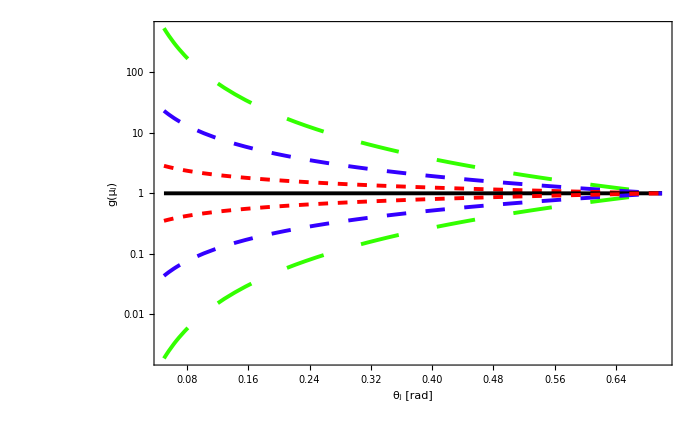

```mathematica
plot1=LogPlot[{gfunc[thetaj,thetaMin,thetaMax,-1.2],gfunc[thetaj,thetaMin,thetaMax,-.6],
gfunc[thetaj,thetaMin,thetaMax,-0.2],gfunc[thetaj,thetaMin,thetaMax,0],
gfunc[thetaj,thetaMin,thetaMax,1.2],gfunc[thetaj,thetaMin,thetaMax,.6],
gfunc[thetaj,thetaMin,thetaMax,0.2]},{thetaj,thetaMin,thetaMax},
PlotStyle->{{Hue[.3],Dashing[{.04}],Thickness[0.004]},
{Hue[.7],Dashing[{.02}],Thickness[0.004]},
{Hue[0],Dashing[{0.01}],Thickness[0.004]},{Hue[0,0,0],Thickness[0.004]}},
Frame->True,FrameLabel->{"θ_j [rad]","g(μ_j)","",""},LabelStyle->{FontSize->15},PlotRange->All,ImageSize->700]
```

```mathematica
label3:= Graphics[{Text["s = 0 ",{0.08,0.2}],
Text[" -0.2 ",{0.1,1.1}],
Text[" -0.6 ",{0.15,2.2}],
Text[" -1.2 ",{0.2,3.4}],
Text[" 0.2 ",{0.1,-1.1}],
Text[" 0.6 ",{0.15,-2.2}],
Text[" 1.2 ",{0.2,-3.4}]}];
```

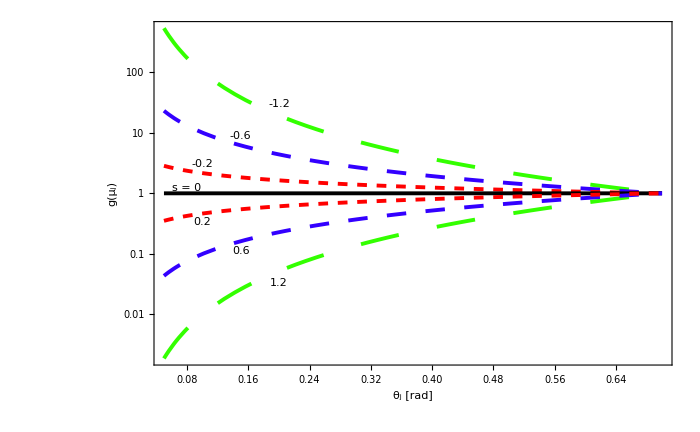

```mathematica
fig3=Show[plot1,label3,BaseStyle->{FontSize->15}]
```

The above curves suggest that (s < 0 ) implies that the fraction of bursts with small jet opening angles increases with decreasing values of s < 0, which is consistent with the beaming effect and this exactly what we want. Where as when (s > 0) the curves suggest that we expect less GRBs at small jet opening angles.

## Below is a plot of the directional event rate per unit redshift [one event per (10^28 cm)^3 per day per sr per z] at H0 = 68,70,72,80,90,100 for SFR11.

#### Hubble constant 68

```mathematica
{H0=68*h0,Estar0=4.47*10^51.,sfr0=11,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.19355×10^-18,4.47×10^51,11,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH68=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

1.34733×10^-6

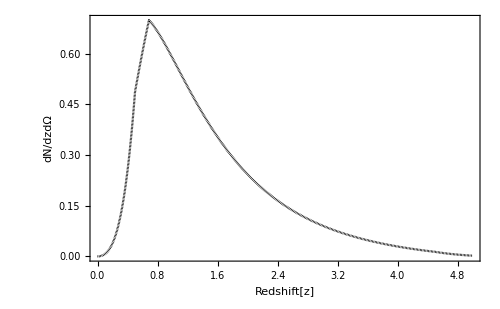

```mathematica
dNdzdOmegaPlotH68=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH68,{z,0,5},PlotStyle -> {Hue[0, 0, 0],Dashing[0.0]}, Frame -> True, Axes -> False, FrameLabel->{"Redshift[z]","dṄ/dzdΩ ",""," "},BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

#### Hubble constant 72

```mathematica
{H0=72*h0,Estar0=4.47*10^51.,sfr0=11,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.32258×10^-18,4.47×10^51,11,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH72=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

1.21146×10^-6

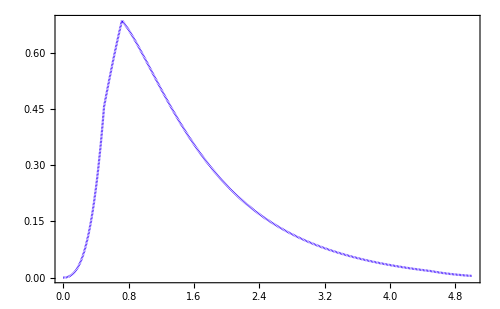

```mathematica
dNdzdOmegaPlotH72=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH72,{z,0,5},PlotStyle -> {Hue[0.7],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

#### Hubble constant 75

```mathematica
{H0=75*h0,Estar0=4.47*10^51.,sfr0=11,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.41935×10^-18,4.47×10^51,11,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH75=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

1.12142×10^-6

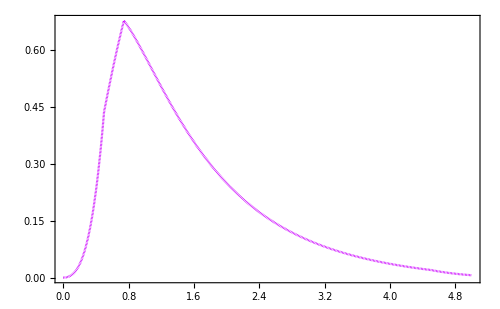

```mathematica
dNdzdOmegaPlotH75=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH75,{z,0,5},PlotStyle -> {Hue[0.8],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

#### Hubble constant 80

```mathematica
{H0=80*h0,Estar0=4.47*10^51.,sfr0=11,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.58065×10^-18,4.47×10^51,11,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH80=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

9.90442×10^-7

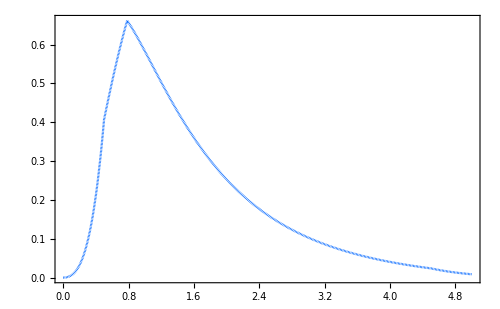

```mathematica
dNdzdOmegaPlotH80=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH80,{z,0,5},PlotStyle -> {Hue[0.6],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

#### Hubble constant 90

```mathematica
{H0=90*h0,Estar0=4.47*10^51.,sfr0=11,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.90323×10^-18,4.47×10^51,11,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH90=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

7.84682×10^-7

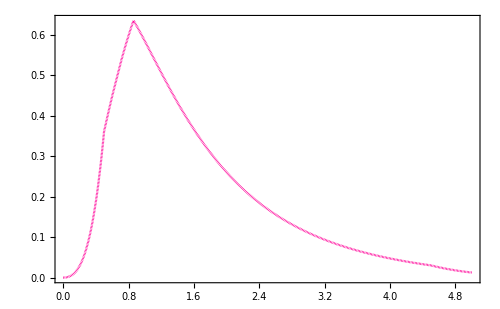

```mathematica
dNdzdOmegaPlotH90=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH90,{z,0,5},PlotStyle -> {Hue[0.9],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

#### Hubble constant 100

```mathematica
{H0=100*h0,Estar0=4.47*10^51.,sfr0=11,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{3.22581×10^-18,4.47×10^51,11,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH100=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

6.33129×10^-7

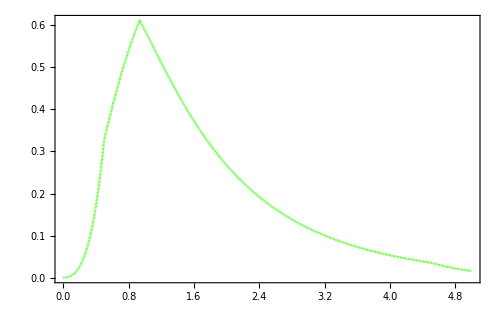

```mathematica
dNdzdOmegaPlotH100=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH100,{z,0,5},PlotStyle -> {Hue[0.3],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

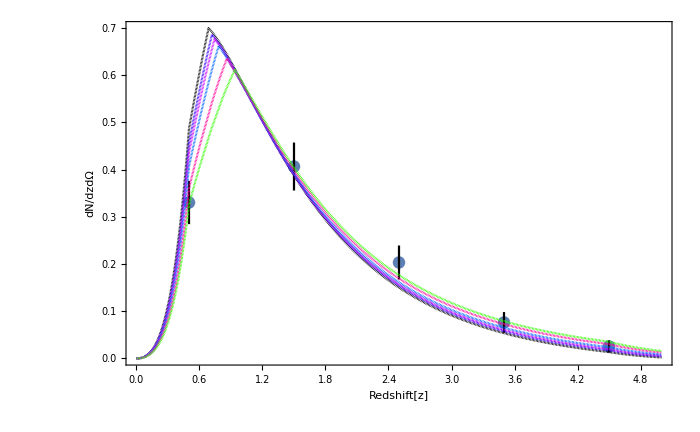

```mathematica
preSwiftPlot6=Show[dataPlot,dNdzdOmegaPlotH68,dNdzdOmegaPlotH72,dNdzdOmegaPlotH75,dNdzdOmegaPlotH80,dNdzdOmegaPlotH90,dNdzdOmegaPlotH100,PlotRange->All]
```

```mathematica
redshiftLabel6 := Graphics[{Text["(a)",{4.7,0.7}],Text["preSwift",{4.5,0.63}],,Text["SFR11",{4.55,0.56}]}];
```

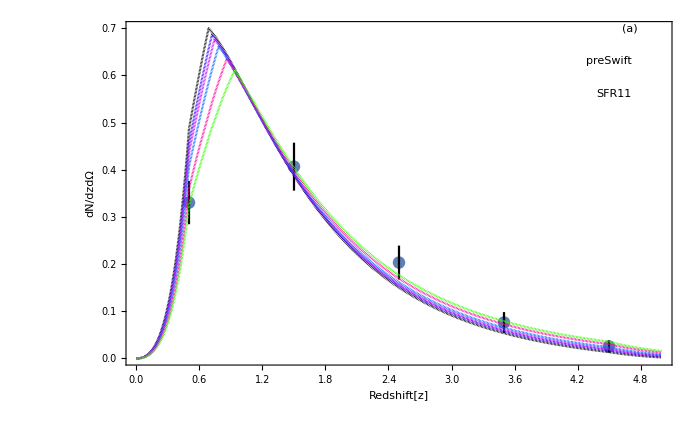

```mathematica
preSwiftBurstRatePerRedshiftPlot=Show[preSwiftPlot6,redshiftLabel6]
```

```mathematica
Export["figure6a.eps", preSwiftBurstRatePerRedshiftPlot, "eps"]
```

figure6a.eps

If we hold everything the same and varied only the Hubble constant and assuming that the 
LGRBs data are complete, then the above results suggest that:
(1) the Hubble constant H0 = 90-100 fits the differential burst rate per redshift the best  as well for the preSwift data, and
(2) if we accept that the hubble constant is any values between H0=68-75, then this would also suggest 
there is deficiency in the GRBs near a redshift of 1.0  or
(3) there is too much GRBs rate near a redshift 1.0 

-Graphics-

Assume that the conclusion one is incorrect and that there is something else in the model could effect this result. As we can see, if the 
jet opening angle distribution can be negatively smaller, then maybe we can fit the model. The next thing that we need to study is
by making s = -1.6 and -1.65. We expect that this reduce the burst rate per redshift, but at the same time it would also reduce the GRBs rate below and above a redshift of 1.2 as well, and this would not fit any data points and a redshift of .5 and above 2.
  -Graphics-

## Below is a plot of the directional event rate per unit redshift [one event per (10^28 cm)^3 per day per sr per z] at H0 = 68,70,72,80,90 assuming that GRBs burst rate follows SFR = 7

#### Hubble constant 68

```mathematica
{H0=68*h0,Estar0=4.47*10^51.,sfr0=7,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.19355×10^-18,4.47×10^51,7,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH68=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

1.19815×10^-6

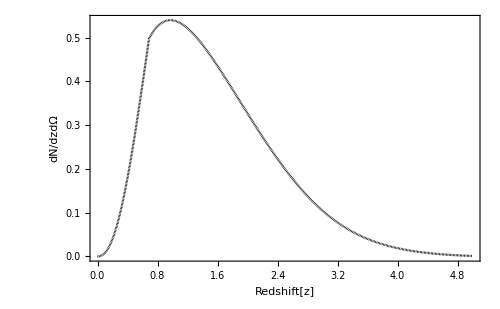

```mathematica
dNdzdOmegaPlotH68=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH68,{z,0,5},PlotStyle -> {Hue[0, 0, 0],Dashing[0.0]}, Frame -> True, Axes -> False, FrameLabel->{"Redshift[z]","dṄ/dzdΩ ",""," "},BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

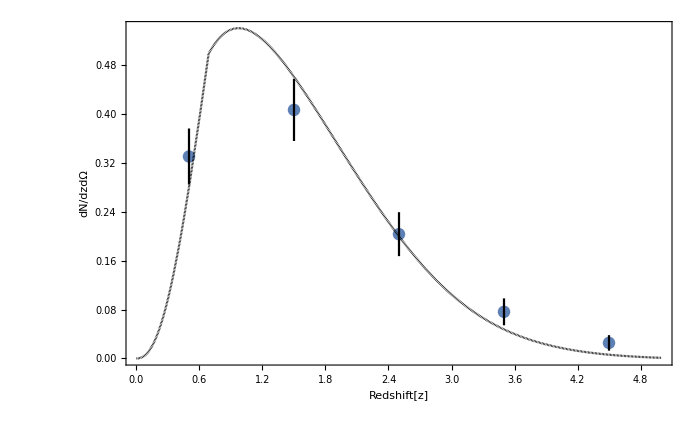

```mathematica
Show[dataPlot,dNdzdOmegaPlotH68,PlotRange->All]
```

#### Hubble constant 70

```mathematica
{H0=70*h0,Estar0=4.47*10^51.,sfr0=7,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.25806×10^-18,4.47×10^51,7,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH70=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

1.13751×10^-6

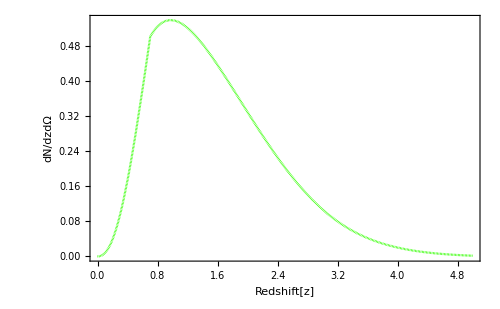

```mathematica
dNdzdOmegaPlotH70=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH70,{z,0,5},PlotStyle -> {Hue[0.3],Dashing[0.0]}, Frame -> True, Axes -> False,FrameLabel->{"Redshift[z]","dṄ/dzdΩ ",""," "}, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

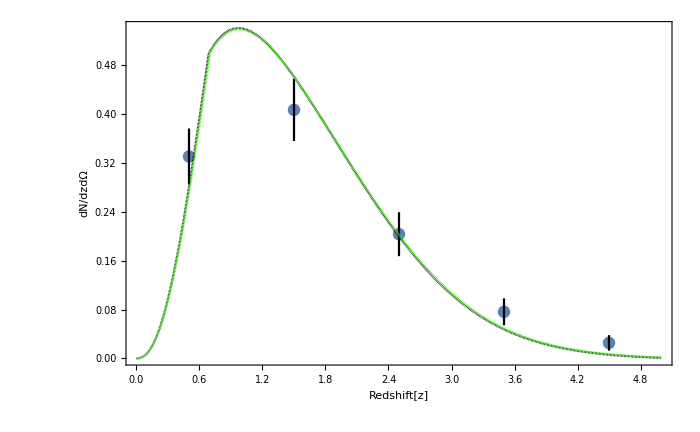

```mathematica
Show[dataPlot,dNdzdOmegaPlotH68,dNdzdOmegaPlotH70,PlotRange->All]
```

#### Hubble constant 72

```mathematica
{H0=72*h0,Estar0=4.47*10^51.,sfr0=11,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.32258×10^-18,4.47×10^51,11,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH72=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

1.21146×10^-6

```mathematica
dNdzdOmegaPlotH72=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH72,{z,0,5},PlotStyle -> {Hue[0.7],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

-Graphics-

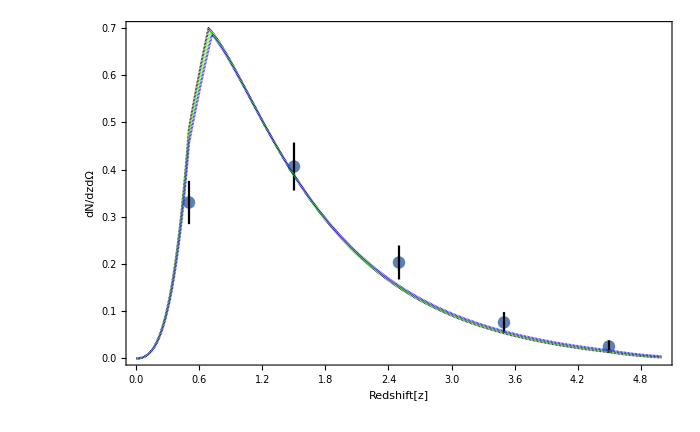

```mathematica
Show[dataPlot,dNdzdOmegaPlotH68,dNdzdOmegaPlotH70,dNdzdOmegaPlotH72,PlotRange->All]
```

#### Hubble constant 75

```mathematica
{H0=75*h0,Estar0=4.47*10^51.,sfr0=7,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.41935×10^-18,4.47×10^51,7,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH75=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

1.00307×10^-6

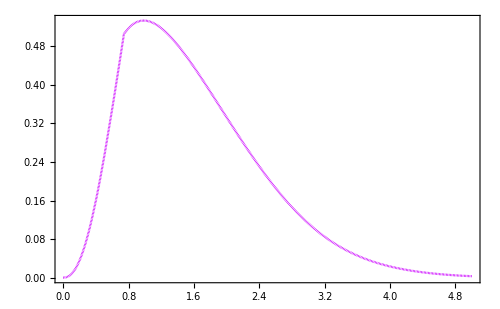

```mathematica
dNdzdOmegaPlotH75=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH75,{z,0,5},PlotStyle -> {Hue[0.8],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

#### Hubble constant 80

```mathematica
{H0=80*h0,Estar0=4.47*10^51.,sfr0=7,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.58065×10^-18,4.47×10^51,7,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH80=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

8.8942×10^-7

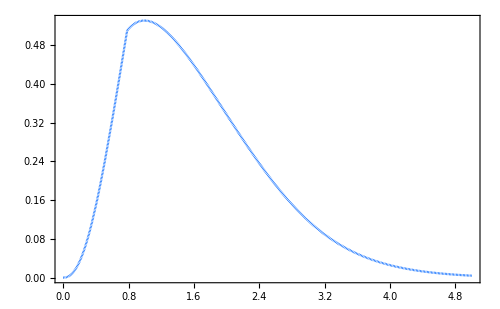

```mathematica
dNdzdOmegaPlotH80=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH80,{z,0,5},PlotStyle -> {Hue[0.6],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

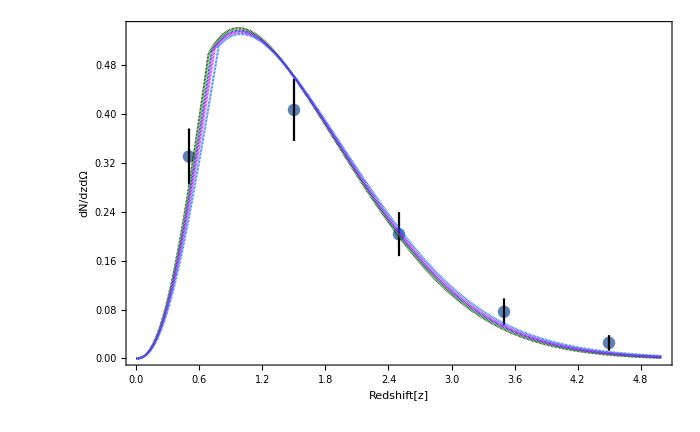

```mathematica
preSwiftPlot7=Show[dataPlot,dNdzdOmegaPlotH68,dNdzdOmegaPlotH70,dNdzdOmegaPlotH72,dNdzdOmegaPlotH75,dNdzdOmegaPlotH80,PlotRange->All]
```

```mathematica
redshiftLabel7 := Graphics[{Text["(a)",{4.8,0.54}],Text["preSwift",{4.5,0.48}],,Text["SFR7",{4.6,0.43}]}];
```

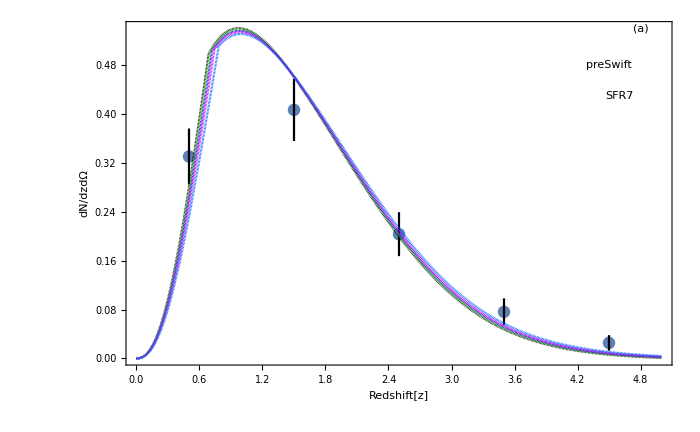

```mathematica
preSwiftBurstRatePerRedshiftPlot=Show[preSwiftPlot7,redshiftLabel7]
```

```mathematica
Export["figure4a.eps", preSwiftBurstRatePerRedshiftPlot, "eps"]
```

From the above results, it is clear that GRB burst rate does not follow SFR. Assuming GRB follows SFR, the result suggests that there should be more GRB rate per redshift below a redshift of 1, less GRB rate per redshift at redshifts between 1-2.5, and there should be more GRB rate per redshift above a redshift 3.5; Indicate that it is not sensitive to different values of the Hubble constant.

## Below is a plot of the directional event rate per unit redshift [one event per (10^28 cm)^3 per day per sr per z] at H0 = 68,70,72,80,90 assuming that GRBs burst rate follows SFR = 9

#### Hubble constant 68

```mathematica
{H0=68*h0,Estar0=4.47*10^51.,sfr0=9,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.19355×10^-18,4.47×10^51,9,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH68=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

9.33324×10^-7

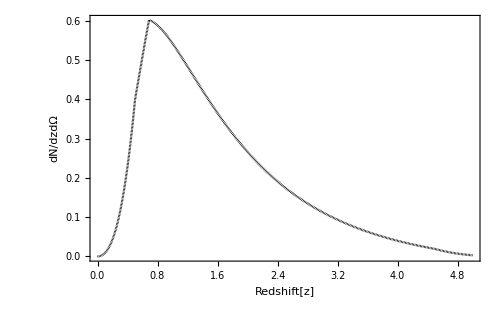

```mathematica
dNdzdOmegaPlotH68=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH68,{z,0,5},PlotStyle -> {Hue[0, 0, 0],Dashing[0.0]}, Frame -> True, Axes -> False, FrameLabel->{"Redshift[z]","dṄ/dzdΩ ",""," "},BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

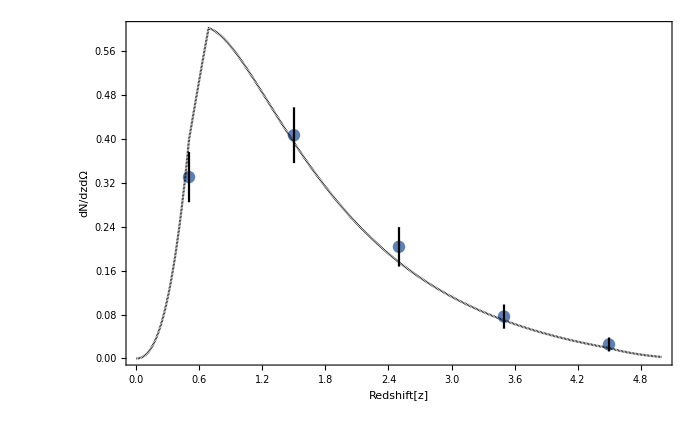

```mathematica
Show[dataPlot,dNdzdOmegaPlotH68,PlotRange->All]
```

#### Hubble constant 70

```mathematica
{H0=70*h0,Estar0=4.47*10^51.,sfr0=9,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.25806×10^-18,4.47×10^51,9,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH70=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

8.86872×10^-7

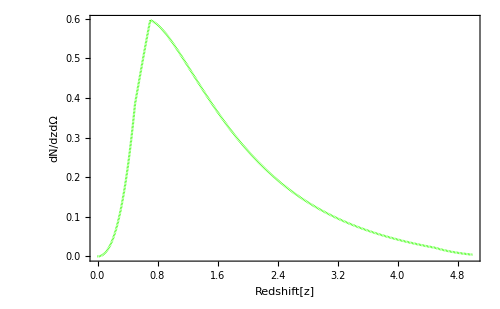

```mathematica
dNdzdOmegaPlotH70=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH70,{z,0,5},PlotStyle -> {Hue[0.3],Dashing[0.0]}, Frame -> True, Axes -> False,FrameLabel->{"Redshift[z]","dṄ/dzdΩ ",""," "}, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

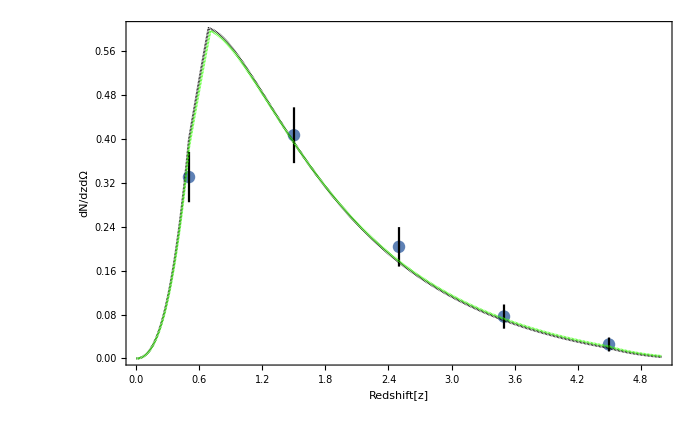

```mathematica
Show[dataPlot,dNdzdOmegaPlotH68,dNdzdOmegaPlotH70,PlotRange->All]
```

#### Hubble constant 72

```mathematica
{H0=72*h0,Estar0=4.47*10^51.,sfr0=9,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.32258×10^-18,4.47×10^51,9,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH72=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

8.43437×10^-7

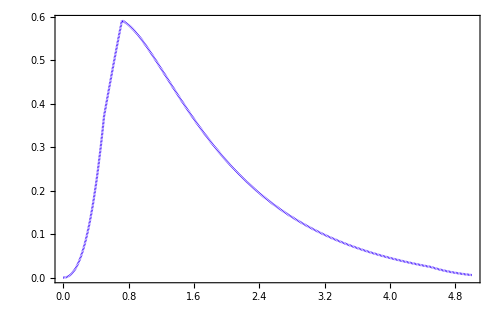

```mathematica
dNdzdOmegaPlotH72=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH72,{z,0,5},PlotStyle -> {Hue[0.7],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

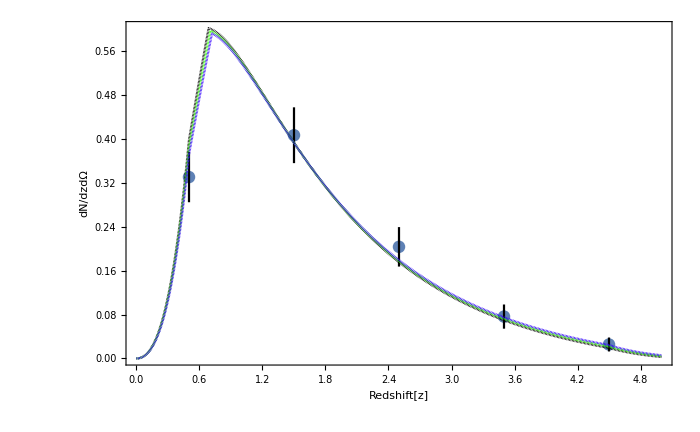

```mathematica
Show[dataPlot,dNdzdOmegaPlotH68,dNdzdOmegaPlotH70,dNdzdOmegaPlotH72,PlotRange->All]
```

#### Hubble constant 75

```mathematica
{H0=75*h0,Estar0=4.47*10^51.,sfr0=9,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.41935×10^-18,4.47×10^51,9,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
normH75=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

7.83455×10^-7

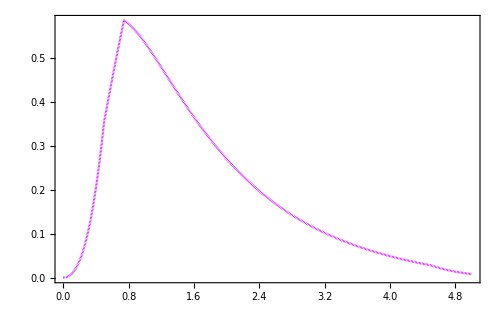

```mathematica
dNdzdOmegaPlotH75=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH75,{z,0,5},PlotStyle -> {Hue[0.8],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

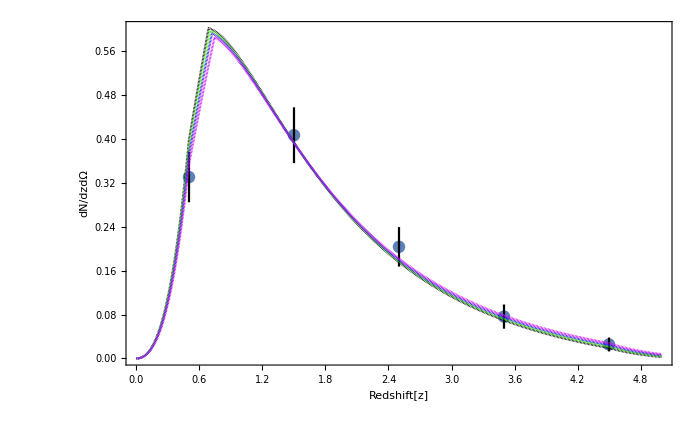

```mathematica
Show[dataPlot,dNdzdOmegaPlotH68,dNdzdOmegaPlotH70,dNdzdOmegaPlotH72,dNdzdOmegaPlotH75,PlotRange->All]
```

#### Hubble constant 80

```mathematica
{H0=80*h0,Estar0=4.47*10^51.,sfr0=9,s0=-1.55,thetajRadMin0=0.065,thetajRadMax0=0.8,deltstar0=10,fthres0=10^-7.,NdensityVal0,k1Val0=6.46464646464646}
```

{2.58065×10^-18,4.47×10^51,9,-1.55,0.065,0.8,10,1.×10^-7,1.1574×10^-89,6.46465}

```mathematica
45*1.25-45
```

11.25

```mathematica
normH80=NIntegrate[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0],{z,0,5}]
```

6.95606×10^-7

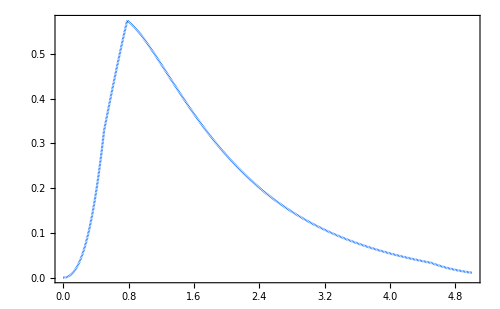

```mathematica
dNdzdOmegaPlotH80=Plot[dNdzdOmega[z,thetajRadMin0,thetajRadMax0,s0,H0,Estar0,deltstar0,fthres0,sfr0,NdensityVal0,k1Val0]/normH80,{z,0,5},PlotStyle -> {Hue[0.6],Dashing[0.0]}, Frame -> True, Axes -> False, BaseStyle -> {FontSize -> 15}, ImageSize -> 500]
```

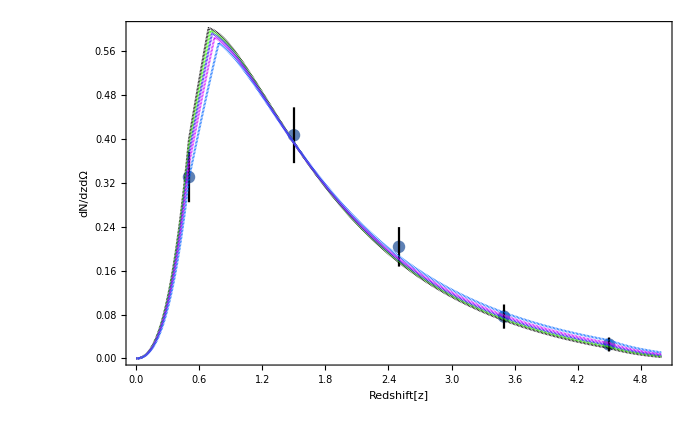

```mathematica
Show[dataPlot,dNdzdOmegaPlotH68,dNdzdOmegaPlotH70,dNdzdOmegaPlotH72,dNdzdOmegaPlotH75,dNdzdOmegaPlotH80,PlotRange->All]
```

```mathematica
preSwiftPlot8=-Graphics-;
```

```mathematica
redshiftLabel8 := Graphics[{Text["(a)",{4.8,0.6}],Text["preSwift",{4.5,0.55}],,Text["SFR9",{4.6,0.50}]}];
```

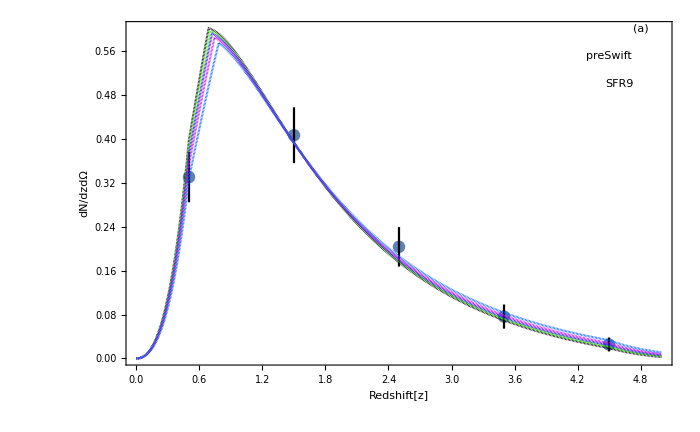

```mathematica
preSwiftBurstRatePerRedshiftPlot=Show[preSwiftPlot8,redshiftLabel8]
```

```mathematica
Export["figure5a.eps", preSwiftBurstRatePerRedshiftPlot, "eps"]
```

From the above results, it indicates that SFR9 is also good, however, there is a strong excess of GRB rate below a redshift 1.
This could suggest that we need another model of GRBs between SFR9 and SFR11. Indicate that it is not sensitive to different values of
the Hubble constant.